```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,n0>=0,d>0,ΔPE+Tpar0 κpar>0,d<1};
FullSimplify[2*Pi*((m^(3/2) n0 Gamma[1+κpar])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar) Gamma[1/2+κpar]))*Integrate[vperp*((√(2 π) Tpar0 ((Tpar0 κpar)/(ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar)) Gamma[κpar]))*((1+(m*d*vperp^2)/(2*κperp*Tperp0))^(-(κperp+1))),{vperp,0,Infinity},Assumptions->assumps2],assumps2]
```

```mathematica
(*Output of Cell above is below in this cell*)

1/d n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (d (ΔPE+Tpar0 κpar))^(1/2+κpar) (-((-1+d) Tperp0 κperp))^κperp (d (ΔPE+Tpar0 κpar)+(-1+d) Tperp0 κperp)^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,-((-1+d) Tperp0 κperp)/(d (ΔPE+Tpar0 κpar))])
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,n0>=0,d>0,ΔPE+Tpar0 κpar>0,d<1};

f=1/d n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (d (ΔPE+Tpar0 κpar))^(1/2+κpar) (-((-1+d) Tperp0 κperp))^κperp (d (ΔPE+Tpar0 κpar)+(-1+d) Tperp0 κperp)^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,-((-1+d) Tperp0 κperp)/(d (ΔPE+Tpar0 κpar))]);
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κ>3/2,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,d>1};
(*Tpar0=50;
Tperp0=100;
B=1;
B0=1;

κpar=4.5;
κperp=2.5;

ΔPE=0;*)
κperp=κ;
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ=(λ0*A0*(d-1))/(ΔPE/(κpar*Tpar0)+1);
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
Limit[d*((λ0*A0*(d-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G),κpar->Infinity,Assumptions->assumps2]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κpar=κ;
κperp=κ;
assumps2={κ>3/2,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,ΔPE+Tpar0 κpar>0,B>B0,δ>0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
(*δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);*)
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((λ0*A0*(B/B0-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

FullSimplify[exprn,assumps2]//TraditionalForm
```

```mathematica
(B (1κ+1/21-κδ-(π (1-δ)^(-2 κ-1/2) δ^κ csc(π κ) 2 κ+1/2)/(κ κ+1/2)) ((Tperp0 (B/B0-1))/(δ Tpar0))^(-κ-1/2))/B0
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
κpar=κ;
κperp=κ;
assumps2={κ>3/2,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,ΔPE+Tpar0 κpar>0,B>B0};
λ0=κperp/κpar;
A0=Tperp0/Tpar0;
δ=(λ0*A0*(B/B0-1))/(ΔPE/(κpar*Tpar0)+1);
G=(Pi*Csc[Pi*κperp]*Gamma[κpar+κperp+1/2]*δ^κperp*(1-δ)^(-κperp-κpar-1/2))/(Gamma[κpar+1/2]*Gamma[κperp]);
exprn=B/B0*((λ0*A0*(B/B0-1))^(-κpar-1/2))*(δ^(κpar+1/2))*(Hypergeometric2F1[1,1/2+κpar,1-κperp,δ] - G);

Simplify[exprn,assumps2]//TraditionalForm
```

```mathematica
1/B0 B (ΔPE/(κ Tpar0)+1)^(-κ-1/2) (1κ+1/21-κ((B-B0) Tperp0 κ)/(B0 (ΔPE+Tpar0 κ))-1/(κ κ+1/2)π csc(π κ) 2 κ+1/2 (κ Tperp0 (B-B0))^κ (B0 (ΔPE+κ Tpar0))^(κ+1/2) (B0 (ΔPE+κ (Tpar0+Tperp0))-B κ Tperp0)^(-2 κ-1/2))
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0};
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,B>0,B0>0,ΔPE∈Reals,Tpar0>0,n0>=0};
E0=ΔPE+1/2*m*vperp^2*(1-B0/B)
FullSimplify[((m^(3/2) n0 Gamma[1+κpar])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar) Gamma[1/2+κpar]))*2*Pi*Integrate[vperp*((√(2 π) Tpar0 ((Tpar0 κpar)/(ΔPE+1/2*m*vperp^2*(1-B0/B)+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (ΔPE+1/2*m*vperp^2*(1-B0/B)+Tpar0 κpar)) Gamma[κpar]))*((1+(m*B0*vperp^2)/(2*κperp*Tperp0*B))^(-(κperp+1))),{vperp,0,Infinity},Assumptions->assumps],assumps2]
```

```mathematica
1/2 (1-B0/B) m vperp^2+ΔPE
ConditionalExpression[1/B0 B n0 ((Tpar0 κpar)/(ΔPE+Tpar0 κpar))^(1/2+κpar) (-((π (B0 (ΔPE+Tpar0 κpar))^(1/2+κpar) ((B-B0) Tperp0 κperp)^κperp (-B Tperp0 κperp+B0 (ΔPE+Tpar0 κpar+Tperp0 κperp))^(-1/2-κpar-κperp) Csc[π κperp] Gamma[1/2+κpar+κperp])/(Gamma[1/2+κpar] Gamma[κperp]))+Hypergeometric2F1[1,1/2+κpar,1-κperp,((B-B0) Tperp0 κperp)/(B0 (ΔPE+Tpar0 κpar))]), B>B0&&ΔPE+Tpar0 κpar>0]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*E0=ΔPE+1/2*m*vperp^2*(1-B0/B)

assumps={κpar>1/2,m>0,Tpar0>0,vperp>=0,B0>0,B>0,ΔPE∈Reals};*)

assumps={κpar>1/2,m>0,Tpar0>0,E0∈Reals};

FullSimplify[Integrate[(1+(m*vpar^2/2+E0)/(κpar*Tpar0))^(-(κpar+1)),{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

```mathematica
ConditionalExpression[(√(2 π) Tpar0 ((Tpar0 κpar)/(E0+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (E0+Tpar0 κpar)) Gamma[κpar]), E0+Tpar0 κpar≥0]
```

-Graphics-

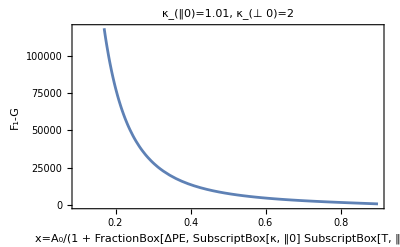

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*0<x<1*)
kappa0=1.01;
kappa1=2.;
kappa2=10.;
kappa3=100.;
kappa4=300.;

κpar0=kappa0;
κperp0=kappa0;
κpar1=kappa1;
κperp1=kappa1;
κpar2=kappa2;
κperp2=kappa2;
κpar3=kappa3;
κperp3=kappa3;
κpar4=kappa4;
κperp4=kappa4;
δ0[x_]:=(κperp0/κpar0)*x;
δ01[x_]:=(κperp1/κpar0)*x;
δ10[x_]:=(κperp0/κpar1)*x;
δ1[x_]:=(κperp1/κpar1)*x;
δ12[x_]:=(κperp2/κpar1)*x;
δ21[x_]:=(κperp1/κpar2)*x;
δ2[x_]:=(κperp2/κpar2)*x;
δ23[x_]:=(κperp3/κpar2)*x;
δ32[x_]:=(κperp2/κpar3)*x;
δ3[x_]:=(κperp3/κpar3)*x;
δ34[x_]:=(κperp4/κpar3)*x;
δ43[x_]:=(κperp3/κpar4)*x;
δ4[x_]:=(κperp4/κpar4)*x;


G0[x_]:=((Pi*(Csc[Pi*κperp0])*Gamma[κpar0+κperp0+0.5])/(Gamma[κpar0+0.5]*Gamma[κperp0]))*(δ0[x]^κperp0)*(δ0[x]^(-κpar0-κperp0-0.5));
f0[x_]:=Hypergeometric2F1[1,1/2+κpar0,1-κperp0,δ0[x]] - G0[x];

G1[x_]:=((Pi*(Csc[Pi*κperp1])*Gamma[κpar0+κperp1+0.5])/(Gamma[κpar0+0.5]*Gamma[κperp1]))*(δ01[x]^κperp1)*(δ01[x]^(-κpar0-κperp1-0.5));
f1[x_]:=Hypergeometric2F1[1,1/2+κpar0,1-κperp1,δ01[x]] - G1[x];

G2[x_]:=((Pi*(Csc[Pi*κperp0])*Gamma[κpar1+κperp0+0.5])/(Gamma[κpar1+0.5]*Gamma[κperp0]))*(δ10[x]^κperp0)*(δ10[x]^(-κpar1-κperp0-0.5));
f2[x_]:=Hypergeometric2F1[1,1/2+κpar1,1-κperp0,δ10[x]] - G2[x];

G3[x_]:=((Pi*(Csc[Pi*κperp1])*Gamma[κpar1+κperp1+0.5])/(Gamma[κpar1+0.5]*Gamma[κperp1]))*(δ1[x]^κperp1)*(δ1[x]^(-κpar1-κperp1-0.5));
f3[x_]:=Hypergeometric2F1[1,1/2+κpar1,1-κperp1,δ1[x]] - G3[x];

G4[x_]:=((Pi*(Csc[Pi*κperp2])*Gamma[κpar1+κperp2+0.5])/(Gamma[κpar1+0.5]*Gamma[κperp2]))*(δ12[x]^κperp2)*(δ12[x]^(-κpar1-κperp2-0.5));
f4[x_]:=Hypergeometric2F1[1,1/2+κpar1,1-κperp2,δ12[x]] - G4[x];

G5[x_]:=((Pi*(Csc[Pi*κperp1])*Gamma[κpar2+κperp1+0.5])/(Gamma[κpar2+0.5]*Gamma[κperp1]))*(δ21[x]^κperp1)*(δ21[x]^(-κpar2-κperp1-0.5));
f5[x_]:=Hypergeometric2F1[1,1/2+κpar2,1-κperp1,δ21[x]] - G5[x];

G6[x_]:=((Pi*(Csc[Pi*κperp2])*Gamma[κpar2+κperp2+0.5])/(Gamma[κpar2+0.5]*Gamma[κperp2]))*(δ2[x]^κperp2)*(δ2[x]^(-κpar2-κperp2-0.5));
f6[x_]:=Hypergeometric2F1[1,1/2+κpar2,1-κperp2,δ2[x]] - G6[x];

G7[x_]:=((Pi*(Csc[Pi*κperp3])*Gamma[κpar2+κperp3+0.5])/(Gamma[κpar2+0.5]*Gamma[κperp3]))*(δ23[x]^κperp3)*(δ23[x]^(-κpar2-κperp3-0.5));
f7[x_]:=Hypergeometric2F1[1,1/2+κpar2,1-κperp3,δ23[x]] - G7[x];


G8[x_]:=((Pi*(Csc[Pi*κperp2])*Gamma[κpar3+κperp2+0.5])/(Gamma[κpar3+0.5]*Gamma[κperp2]))*(δ32[x]^κperp2)*(δ32[x]^(-κpar3-κperp2-0.5));
f8[x_]:=Hypergeometric2F1[1,1/2+κpar3,1-κperp2,δ32[x]] - G8[x];

G9[x_]:=((Pi*(Csc[Pi*κperp3])*Gamma[κpar3+κperp3+0.5])/(Gamma[κpar3+0.5]*Gamma[κperp3]))*(δ3[x]^κperp3)*(δ3[x]^(-κpar3-κperp3-0.5));
f9[x_]:=Hypergeometric2F1[1,1/2+κpar3,1-κperp3,δ3[x]] - G9[x];

G10[x_]:=((Pi*(Csc[Pi*κperp4])*Gamma[κpar3+κperp4+0.5])/(Gamma[κpar3+0.5]*Gamma[κperp4]))*(δ34[x]^κperp4)*(δ34[x]^(-κpar3-κperp4-0.5));
f10[x_]:=Hypergeometric2F1[1,1/2+κpar3,1-κperp4,δ34[x]] - G10[x];

G11[x_]:=((Pi*(Csc[Pi*κperp3])*Gamma[κpar4+κperp3+0.5])/(Gamma[κpar4+0.5]*Gamma[κperp3]))*(δ43[x]^κperp3)*(δ43[x]^(-κpar4-κperp3-0.5));
f11[x_]:=Hypergeometric2F1[1,1/2+κpar4,1-κperp3,δ43[x]] - G11[x];

G12[x_]:=((Pi*(Csc[Pi*κperp4])*Gamma[κpar4+κperp4+0.5])/(Gamma[κpar4+0.5]*Gamma[κperp4]))*(δ4[x]^κperp4)*(δ4[x]^(-κpar4-κperp4-0.5));
f12[x_]:=Hypergeometric2F1[1,1/2+κpar4,1-κperp4,δ4[x]] - G12[x];

Plot[f1[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=1.01, κ_(⊥ 0)=1.01"]
Plot[f2[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=1.01, κ_(⊥ 0)=2"]
Plot[f3[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=2, κ_(⊥ 0)=2"]
Plot[f4[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=2, κ_(⊥ 0)=10"]

Plot[f5[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=10, κ_(⊥ 0)=2"]

Plot[f6[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=10, κ_(⊥ 0)=10"]
Plot[f7[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=10, κ_(⊥ 0)=100"]
Plot[f8[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=100, κ_(⊥ 0)=10"]
Plot[f9[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=100, κ_(⊥ 0)=100"]
Plot[f10[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=100, κ_(⊥ 0)=300"]
Plot[f11[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=300, κ_(⊥ 0)=100"]
Plot[f12[x],{x,0.1,0.9},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","F_1-G"},PlotLabel->" κ_(‖0)=300, κ_(⊥ 0)=300"]
```

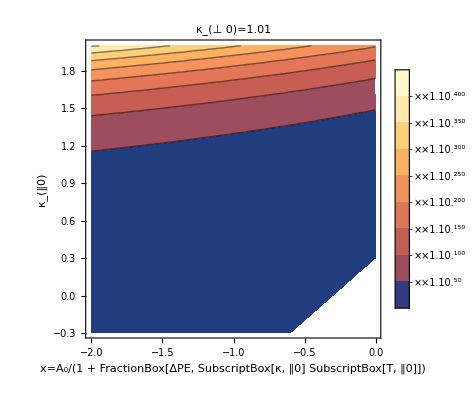

-Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*0<x<1*)
kappa0=1.01;
kappa1=2.;
kappa2=10.;
kappa3=100.;
kappa4=300.;

κpar0=kappa0;
κperp0=kappa0;
κpar1=kappa1;
κperp1=kappa1;
κpar2=kappa2;
κperp2=kappa2;
κpar3=kappa3;
κperp3=kappa3;
κpar4=kappa4;
κperp4=kappa4;
δ0[x_]:=(κperp0/κpar0)*x;
δ01[x_]:=(κperp1/κpar0)*x;
δ10[x_]:=(κperp0/κpar1)*x;
δ1[x_]:=(κperp1/κpar1)*x;
δ12[x_]:=(κperp2/κpar1)*x;
δ21[x_]:=(κperp1/κpar2)*x;
δ2[x_]:=(κperp2/κpar2)*x;
δ23[x_]:=(κperp3/κpar2)*x;
δ32[x_]:=(κperp2/κpar3)*x;
δ3[x_]:=(κperp3/κpar3)*x;
δ34[x_]:=(κperp4/κpar3)*x;
δ43[x_]:=(κperp3/κpar4)*x;
δ4[x_]:=(κperp4/κpar4)*x;


f[x_,κperp_,κpar_]:=Hypergeometric2F1[1,1/2+κpar,1-κperp,κperp/κpar*x] - ((Pi*(Csc[Pi*κperp])*Gamma[κpar+κperp+0.5])/(Gamma[κpar+0.5]*Gamma[κperp]))*((κperp/κpar*x)^κperp)*((κperp/κpar*x)^(-κpar-κperp-0.5));


κperpval=κperp0;
ContourPlot[f[x,κperpval,κpar],{x,0.01,0.99},{κpar,0.51,100},ScalingFunctions->{"Log10","Log10","Log10"},FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","κ_(‖0)"},PlotLabel->"κ_(⊥ 0)="<>ToString[κperpval],PlotLegends->Automatic,PlotRange->All,RegionFunction->Function[{x,y,z},x<y/κperpval]]

κperpval=κperp1;
ContourPlot[f[x,κperpval,κpar],{x,0.01,0.99},{κpar,0.51,100},ScalingFunctions->{"Log10","Log10","Linear"},FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","κ_(‖0)"},PlotLabel->"κ_(⊥ 0)="<>ToString[κperpval],PlotLegends->Automatic,PlotRange->All,RegionFunction->Function[{x,y,z},x<y/κperpval]]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps2={κpar>1/2,κperp>1,m>0,Tperp0>0,ΔPE∈Reals,Tpar0>0,n0>=0,d>0,ΔPE+Tpar0 κpar>0,d<1};
κpar=κ
κperp=κ
FullSimplify[2*Pi*((m^(3/2) n0 Gamma[1+κpar])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar) Gamma[1/2+κpar]))*Integrate[vperp*((√(2 π) Tpar0 ((Tpar0 κpar)/(ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar))^κpar Gamma[1/2+κpar])/(√(m (ΔPE+1/2*m*vperp^2*(1-d)+Tpar0 κpar)) Gamma[κpar]))*((1+(m*d*vperp^2)/(2*κperp*Tperp0))^(-(κperp+1))),{vperp,0,Infinity},Assumptions->assumps2],assumps2]
```

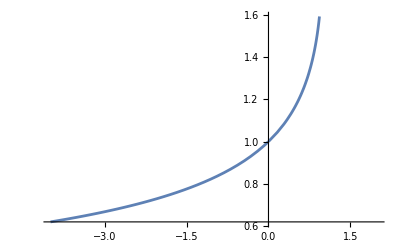

```mathematica
Plot[Hypergeometric2F1Regularized[1/2,1,2,x],{x,-4,2}]
```

```mathematica
Plot[Hypergeometric2F1[1/2,1,2,x],{x,-4,2}]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*Set high precision*)
val=10000;
$MaxExtraPrecision=val;


(*Define parameters with precision*)
kappaPar0=SetPrecision[1.01,val];
kappaPerp0=SetPrecision[2.0,val];

delta[x_]:=(kappaPerp0/kappaPar0)*x;

(*Define the combined function directly to handle cancellation*)
nAlpha[x_]:=Module[{deltaVal=delta[x],hypergeo,G},hypergeo=Hypergeometric2F1Regularized[1,0.5+kappaPar0,1-kappaPerp0,deltaVal];
G=((Pi*Csc[Pi*kappaPerp0]*Gamma[kappaPar0+kappaPerp0+0.5])/(Gamma[kappaPar0+0.5]*Gamma[kappaPerp0]))*deltaVal^kappaPerp0*(1-deltaVal)^(-kappaPar0-kappaPerp0-0.5);
N[hypergeo-G,val]];

Plot[nAlpha[x],{x,0.00000001,0.99999999},WorkingPrecision->val,PlotRange->All]
```

-Graphics-

General::munfl: 0.000304282^100 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.16931×10^-306 0.000304282 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(5.54172×10^-306)/1131 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Plot::precw: The precision of the argument function ({(1-1. x)-1,-1. Im[x]-0}) is less than WorkingPrecision (50.).

Plot::precw: The precision of the argument function ({True,1-1. Re[x]≥1}) is less than WorkingPrecision (50.).

Plot::precw: The precision of the argument function ({(1-1.9802 x)-1,-1.9802 Im[x]-0}) is less than WorkingPrecision (50.).

General::stop: Further output of Plot::precw will be suppressed during this calculation.

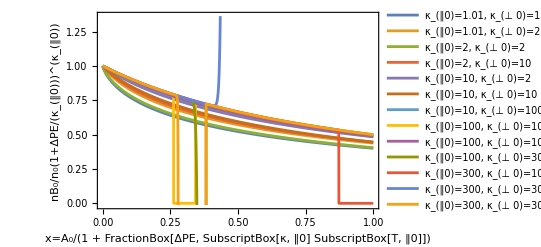

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
val=50;
$MaxExtraPrecision=val;

(*0<x<1*)
kappa0=1.01;
kappa1=2.;
kappa2=10.;
kappa3=100.;
kappa4=300.;

κpar0=kappa0;
κperp0=kappa0;
κpar1=kappa1;
κperp1=kappa1;
κpar2=kappa2;
κperp2=kappa2;
κpar3=kappa3;
κperp3=kappa3;
κpar4=kappa4;
κperp4=kappa4;
δ0[x_]:=(κperp0/κpar0)*x;
δ01[x_]:=(κperp1/κpar0)*x;
δ10[x_]:=(κperp0/κpar1)*x;
δ1[x_]:=(κperp1/κpar1)*x;
δ12[x_]:=(κperp2/κpar1)*x;
δ21[x_]:=(κperp1/κpar2)*x;
δ2[x_]:=(κperp2/κpar2)*x;
δ23[x_]:=(κperp3/κpar2)*x;
δ32[x_]:=(κperp2/κpar3)*x;
δ3[x_]:=(κperp3/κpar3)*x;
δ34[x_]:=(κperp4/κpar3)*x;
δ43[x_]:=(κperp3/κpar4)*x;
δ4[x_]:=(κperp4/κpar4)*x;



f[x_,κpar_,κperp_]:=κperp*(Gamma[κperp+κpar+1/2]/Gamma[κperp+κpar+3/2])*Hypergeometric2F1[1/2+κpar,1,κperp+κpar+3/2,1-κperp/κpar*x] 
xmin=0.00001;
xmax=0.99999;
Plot[{f[x,κpar0,κperp0],f[x,κpar0,κperp1],f[x,κpar1,κperp0],f[x,κpar1,κperp1],f[x,κpar1,κperp2],f[x,κpar2,κperp1],f[x,κpar2,κperp2],f[x,κpar2,κperp3],f[x,κpar3,κperp2],f[x,κpar3,κperp3],f[x,κpar3,κperp4],f[x,κpar4,κperp3],f[x,κpar4,κperp4]},{x,xmin,xmax},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","nB_0/n_0(1+ΔPE/(κ_(‖0)))^(κ_(‖0))"},PlotLegends->{" κ_(‖0)=1.01, κ_(⊥ 0)=1.01"," κ_(‖0)=1.01, κ_(⊥ 0)=2"," κ_(‖0)=2, κ_(⊥ 0)=2"," κ_(‖0)=2, κ_(⊥ 0)=10"," κ_(‖0)=10, κ_(⊥ 0)=2"," κ_(‖0)=10, κ_(⊥ 0)=10"," κ_(‖0)=10, κ_(⊥ 0)=100"," κ_(‖0)=100, κ_(⊥ 0)=10"," κ_(‖0)=100, κ_(⊥ 0)=100"," κ_(‖0)=100, κ_(⊥ 0)=300"," κ_(‖0)=300, κ_(⊥ 0)=100"," κ_(‖0)=300, κ_(⊥ 0)=300"," κ_(‖0)=300, κ_(⊥ 0)=300"},WorkingPrecision->val]
```

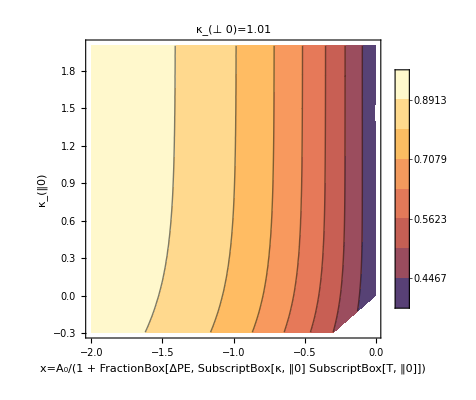

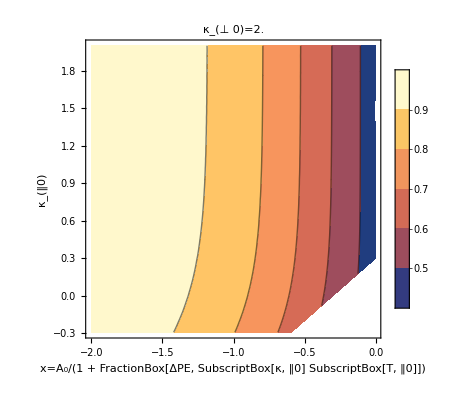

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*0<x<1*)
kappa0=1.01;
kappa1=2.;
kappa2=10.;
kappa3=100.;
kappa4=300.;

κpar0=kappa0;
κperp0=kappa0;
κpar1=kappa1;
κperp1=kappa1;
κpar2=kappa2;
κperp2=kappa2;
κpar3=kappa3;
κperp3=kappa3;
κpar4=kappa4;
κperp4=kappa4;
δ0[x_]:=(κperp0/κpar0)*x;
δ01[x_]:=(κperp1/κpar0)*x;
δ10[x_]:=(κperp0/κpar1)*x;
δ1[x_]:=(κperp1/κpar1)*x;
δ12[x_]:=(κperp2/κpar1)*x;
δ21[x_]:=(κperp1/κpar2)*x;
δ2[x_]:=(κperp2/κpar2)*x;
δ23[x_]:=(κperp3/κpar2)*x;
δ32[x_]:=(κperp2/κpar3)*x;
δ3[x_]:=(κperp3/κpar3)*x;
δ34[x_]:=(κperp4/κpar3)*x;
δ43[x_]:=(κperp3/κpar4)*x;
δ4[x_]:=(κperp4/κpar4)*x;


f[x_,κperp_,κpar_]:=κperp*(Gamma[κperp+κpar+1/2]/Gamma[κperp+κpar+3/2])*Hypergeometric2F1[1/2+κpar,1,κperp+κpar+3/2,1-κperp/κpar*x] 


κperpval=κperp0;
ContourPlot[f[x,κperpval,κpar],{x,0.01,0.99},{κpar,0.51,100},ScalingFunctions->{"Log10","Log10","Log10"},FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","κ_(‖0)"},PlotLabel->"κ_(⊥ 0)="<>ToString[κperpval],PlotLegends->Automatic,PlotRange->All,RegionFunction->Function[{x,y,z},x<y/κperpval]]

κperpval=κperp1;
ContourPlot[f[x,κperpval,κpar],{x,0.01,0.99},{κpar,0.51,100},ScalingFunctions->{"Log10","Log10","Linear"},FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","κ_(‖0)"},PlotLabel->"κ_(⊥ 0)="<>ToString[κperpval],PlotLegends->Automatic,PlotRange->All,RegionFunction->Function[{x,y,z},x<y/κperpval]]
```

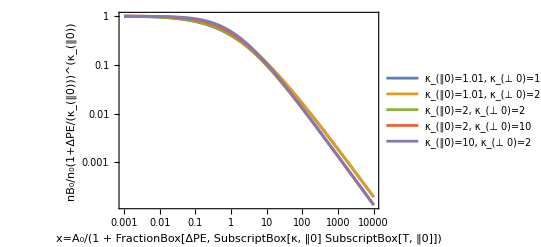

General::munfl: (5.10214×10^-207)/93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.93816×10^-207)/93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

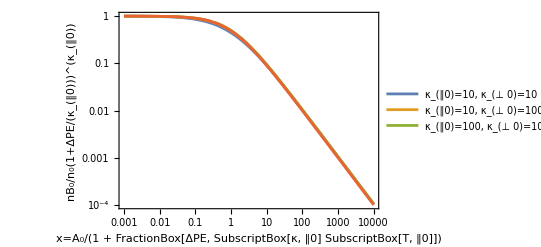

General::munfl: (1.03348×10^-300)/(9.32096×10^156) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.998986 1.79431129740451×10^-376 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.99533×10^-286)/(9.32096×10^156) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::infy: Infinite expression -3.14159/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

-Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*val=00;
$MaxExtraPrecision=val;*)


(*0<x<1*)
kappa0=1.01;
kappa1=2.;
kappa2=10.;
kappa3=100.;
kappa4=300.;

κpar0=kappa0;
κperp0=kappa0;
κpar1=kappa1;
κperp1=kappa1;
κpar2=kappa2;
κperp2=kappa2;
κpar3=kappa3;
κperp3=kappa3;
κpar4=kappa4;
κperp4=kappa4;
δ0[x_]:=(κperp0/κpar0)*x;
δ01[x_]:=(κperp1/κpar0)*x;
δ10[x_]:=(κperp0/κpar1)*x;
δ1[x_]:=(κperp1/κpar1)*x;
δ12[x_]:=(κperp2/κpar1)*x;
δ21[x_]:=(κperp1/κpar2)*x;
δ2[x_]:=(κperp2/κpar2)*x;
δ23[x_]:=(κperp3/κpar2)*x;
δ32[x_]:=(κperp2/κpar3)*x;
δ3[x_]:=(κperp3/κpar3)*x;
δ34[x_]:=(κperp4/κpar3)*x;
δ43[x_]:=(κperp3/κpar4)*x;
δ4[x_]:=(κperp4/κpar4)*x;



f[x_,κpar_,κperp_]:=κperp*(Gamma[κperp+κpar+1/2])*Hypergeometric2F1Regularized[1/2+κpar,1,κperp+κpar+3/2,1-κperp/κpar*x] 
xmin=0.001;
xmax=10^4;
LogLogPlot[{f[x,κpar0,κperp0],f[x,κpar0,κperp1],f[x,κpar1,κperp0],f[x,κpar1,κperp1],f[x,κpar1,κperp2]},{x,xmin,xmax},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","nB_0/n_0(1+ΔPE/(κ_(‖0)))^(κ_(‖0))"},PlotLegends->{" κ_(‖0)=1.01, κ_(⊥ 0)=1.01"," κ_(‖0)=1.01, κ_(⊥ 0)=2"," κ_(‖0)=2, κ_(⊥ 0)=2"," κ_(‖0)=2, κ_(⊥ 0)=10"," κ_(‖0)=10, κ_(⊥ 0)=2"}](*,WorkingPrecision->val]*)

LogLogPlot[{f[x,κpar2,κperp1],f[x,κpar2,κperp2],f[x,κpar2,κperp3],f[x,κpar3,κperp2]},{x,xmin,xmax},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","nB_0/n_0(1+ΔPE/(κ_(‖0)))^(κ_(‖0))"},PlotLegends->{" κ_(‖0)=10, κ_(⊥ 0)=10"," κ_(‖0)=10, κ_(⊥ 0)=100"," κ_(‖0)=100, κ_(⊥ 0)=10"}](*,WorkingPrecision->val]*)


LogLogPlot[{f[x,κpar3,κperp3],f[x,κpar3,κperp4],f[x,κpar4,κperp3],f[x,κpar4,κperp4]},{x,xmin,xmax},Frame->True,FrameLabel->{"x=A_0/(1 + FractionBox[ΔPE, SubscriptBox[κ, ‖0] SubscriptBox[T, ‖0]])","nB_0/n_0(1+ΔPE/(κ_(‖0)))^(κ_(‖0))"},PlotLegends->{" κ_(‖0)=100, κ_(⊥ 0)=100"," κ_(‖0)=100, κ_(⊥ 0)=300"," κ_(‖0)=300, κ_(⊥ 0)=100"," κ_(‖0)=300, κ_(⊥ 0)=300"}](*,WorkingPrecision->val]*)
```

```mathematica
Gamma[1]
```

1

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={μ>2,ν>1}
FullSimplify[Gamma[μ+ν-1]*Gamma[ν],assumps]
```

{μ>2,ν>1}

Gamma[ν] Gamma[-1+μ+ν]

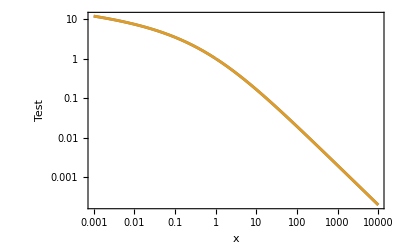

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
a=2;
b=1;
c=3;
LogLogPlot[{Hypergeometric2F1[a,b,c,1-x],(Gamma[c])*Hypergeometric2F1Regularized[a,b,c,1-x]},{x,0.001,10000},FrameLabel->{"x","Test"},Frame->True]
```

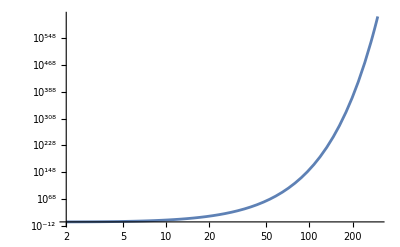

```mathematica
LogLogPlot[Gamma[x],{x,2,300}]
```

```mathematica
AsymptoticSolve[y==Gamma[x],y,{x,Infinity,1},Reals]
```

{{y→Gamma[x]}}

```mathematica
FullSimplify[Series[Gamma[1/y],{y,0,2}],{0<=y<2}]
```

ⅇ^((-1-Log[y])/y+1/2 (Log[2]+Log[π]+Log[y])+y/12+O[y]^3)

```mathematica
(*Gamma[x]~ Exp[(-1-Log[1/x])/(1/x)+1/2 (Log[2]+Log[π]+Log[1/x])+1/(12*x)], for large x=kappaperp + kappapar + 1/2*)
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

FullSimplify[Series[1/ηperp*(Gamma[1/ηperp+1/ηpar+1/2])*Hypergeometric2F1Regularized[1/2+1/ηpar,1,1/ηperp+1/ηpar+3/2,1-ηpar/ηperp*x] ,{ηpar,0,1},{ηperp,0,1},Assumptions->{x>=0}],Assumptions->{x>=0,0<=ηperp<1,0<=ηpar<2}]
```

ⅇ^(-1/ηpar+1/2 Log[2 π]+(1/(2 ηperp^2)-1/24+O[ηperp]^2) ηpar+O[ηpar]^2) ηpar^(-(ηpar+ηperp)/(ηpar ηperp)) Hypergeometric2F1Regularized[1,1/2+1/ηpar,3/2+1/ηpar+1/ηperp,1-(x ηpar)/ηperp] ((1/ηperp+O[ηperp]^2)+O[ηpar]^2)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

FullSimplify[Series[Hypergeometric2F1Regularized[1/2+1/ηpar,1,1/ηperp+1/ηpar+3/2,1-ηpar/ηperp*x] ,{ηpar,0,1},Assumptions->{x>=0,0<=ηperp<1}],Assumptions->{x>=0,0<=ηperp<1,0<=ηpar<2}]
```

Hypergeometric2F1Regularized[1,1/2+1/ηpar,3/2+1/ηpar+1/ηperp,1-(x ηpar)/ηperp]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*z=1-δ*)
Series[(1-t)^(1/crecip-2),{crecip,0,1},Assumptions->{0<=t<=1}]
Series[(1-t*z)^(1/arecip),{arecip,0,1},Assumptions->{0<=t<=1,z<=1}]
```

(1-t)^(1/crecip-2+O[crecip]^2)

(1-t z)^(1/arecip+O[arecip]^2)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={z<=1,a>1,c>3};
Integrate[(1-t)^(c-2)*(1-t*z)^-a,{t,0,1},Assumptions->assumps]
Integrate[(1-t)^(κpar+κperp)*(1-t*z)^-κpar,{t,0,1},Assumptions->{κperp>17,κpar>17,z<=1}]
```

Hypergeometric2F1[1,a,c,z]/(-1+c)

Hypergeometric2F1[1,κpar,2+κpar+κperp,z]/(1+κpar+κperp)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={z<=1,a>1,c>3};
FullSimplify[Hypergeometric2F1[1,a,c,z]/(-1+c)==Gamma[c-1]*Hypergeometric2F1Regularized[a,1,c,z],assumps]
```

True

```mathematica
Series[(1-t*z)^(-1/recipκpar),{recipκpar,0,1},Assumptions->{0<=t<=1,z<=1}]
```

(1-t z)^(-1/recipκpar+O[recipκpar]^2)

```mathematica
Series[(1-t)^(1/recipκtot),{recipκtot,0,1},Assumptions->{0<=t<=1,z<=1}]
```

(1-t)^(1/recipκtot+O[recipκtot]^2)

```mathematica
Series[(1-t*z)^-κpar,{κpar,Infinity,1},Assumptions->{0<=t<=1,z<=1}]
```

(1-t z)^(-κpar+O[1/κpar]^2)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[Solve[(-(κperp+κpar - 1/2))/(1-t)+(z*(κpar+1/2))/(1-t*z)==0,t,Assumptions->{z<=1,κpar>0.5,κperp>1}],{z<=1,κpar>0.5,κperp>1}]
```

{{t→(1+z-2 κpar+2 z κpar-2 κperp)/(2 z-2 z κperp)}}

```mathematica
Series[(1+z-2 κpar+2 z κpar-2 κperp)/(2 z-2 z κperp),{}]
```

```mathematica
Series[(1-ϵ)^-1,{ϵ,0,1}]
```

1+ϵ+O[ϵ]^2

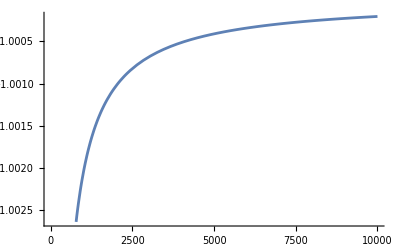

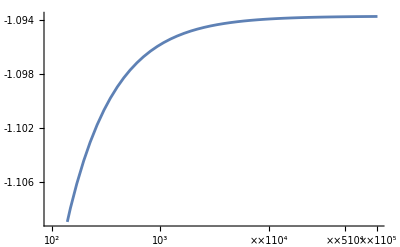

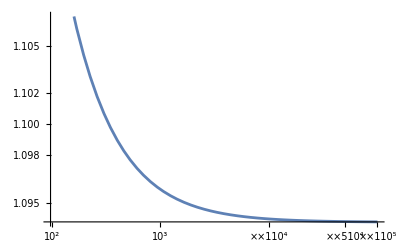

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Plot[2/(1-δ)-1+1/(17*(1-δ)),{δ,0,10000}]

κpar=17;
κperp=17;
Plot[(1+(1-δ)-2 κpar+2 (1-δ) κpar-2 κperp)/(2 (1-δ)-2 (1-δ) κperp),{δ,0,100000},ScalingFunctions->{"Log10","Linear"}]
Plot[Abs[(1+(1-δ)-2 κpar+2 (1-δ) κpar-2 κperp)/(2 (1-δ)-2 (1-δ) κperp)],{δ,0,100000},ScalingFunctions->{"Log10","Log10"}]
```

{{t→(κpar-z κpar+κperp)/(z κperp)}}

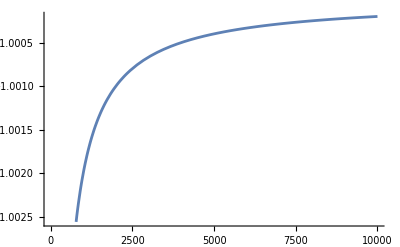

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[Solve[(-(κperp+κpar ))/(1-t)+(z*(κpar))/(1-t*z)==0,t,Assumptions->{z<=1,κpar>0.5,κperp>1}],{z<=1,κpar>0.5,κperp>1}]
κpar=17;
κperp=17;
Plot[(κpar-(1-δ) κpar+κperp)/((1-δ) κperp),{δ,0,10000}]
```

```mathematica
Series[Sin[x]^3,{x,0,3}]
```

x^3+O[x]^4

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Series[Log[1-t],{t,0,3}]
```

-t-t^2/2-t^3/3+O[t]^4

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>15,κperp>15,z<=1};

FullSimplify[Integrate[Exp[-(κpar+κperp)*(t)+κpar*(t*z)],{t,0,1},Assumptions->assumps],assumps]
FullSimplify[Integrate[Exp[-(κpar+κperp)*(t)+κpar*(t*z+t^2*z^2/2)],{t,0,1},Assumptions->assumps],assumps]

FullSimplify[Integrate[Exp[-(κpar+κperp-1/2)*(t+t^2/2)+(κpar+1/2)*(t*z+t^2*z^2/2)],{t,0,1},Assumptions->assumps],assumps]


FullSimplify[Integrate[Exp[-(κpar+κperp-1/2)*(t)+(κpar+1/2)*(t*z)],{t,0,1},Assumptions->assumps],assumps]
```

(1-ⅇ^((-1+z) κpar-κperp))/(κpar-z κpar+κperp)

(√2 (-DawsonF[((-1+z) κpar-κperp)/(√2 z √κpar)]+ⅇ^((-1+z+z^2/2) κpar-κperp) DawsonF[((-1+z+z^2) κpar-κperp)/(√2 z √κpar)]))/(z √κpar)

(ⅇ^(-(1+z-2 κpar+2 z κpar-2 κperp)^2/(4-8 κpar+z^2 (4+8 κpar)-8 κperp)) √π (-Erf[(2-4 κpar+z (1+z) (1+2 κpar)-4 κperp)/(2 √(-1+2 κpar-z^2 (1+2 κpar)+2 κperp))]+Erf[(1+z-2 κpar+2 z κpar-2 κperp)/(2 √(-1+2 κpar-z^2 (1+2 κpar)+2 κperp))]))/(√(-1+2 κpar-z^2 (1+2 κpar)+2 κperp))

(2 (-1+ⅇ^(1/2 (1+z-2 κpar+2 z κpar-2 κperp))))/(1+z-2 κpar+2 z κpar-2 κperp)

```mathematica
Series[(1-t)^(-1/2),{t,0,2}]
```

1+t/2+(3 t^2)/8+O[t]^3

```mathematica
ExpandAll[(1+t/2+(3 t^2)/8)*(1+(t*z)/2+(3 (t*z)^2)/8)]
```

1+t/2+(3 t^2)/8+(t z)/2+(t^2 z)/4+(3 t^3 z)/16+(3 t^2 z^2)/8+(3 t^3 z^2)/16+(9 t^4 z^2)/64

```mathematica
ExpandAll[(1-t)*(1-t*z)]
```

1-t-t z+t^2 z

```mathematica
Series[(1-t-t z+t^2 z)^(1/2),{t,0,1},{z,0,1}]
```

1+(-1/2-z/2+O[z]^2) t+O[t]^2

```mathematica
Series[(1-t-t z+t^2 z)^(1/2),{z,0,1},{t,0,1}]
```

(1-t/2+O[t]^2)+(-t/2+O[t]^2) z+O[z]^2

```mathematica
Series[Log[1/(1-t)],{t,0,2}]
Series[Log[1/(1-t*(1-δ))],{t,0,2},Assumptions->δ>=0]
```

t+t^2/2+O[t]^3

(1-δ) t+1/2 (1-2 δ+δ^2) t^2+O[t]^3

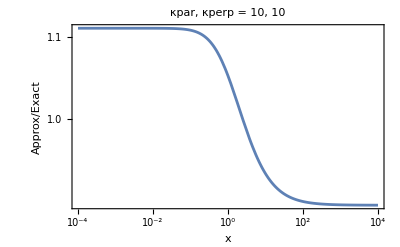
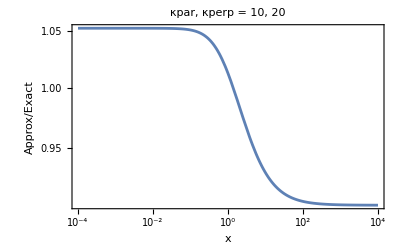
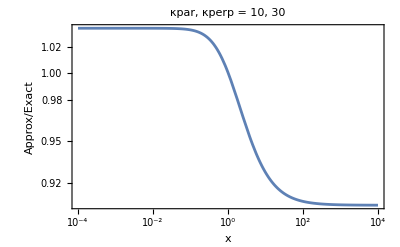
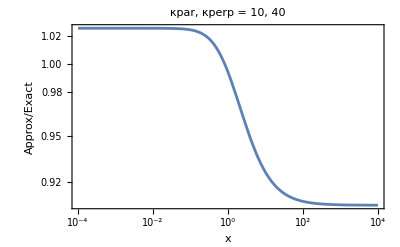
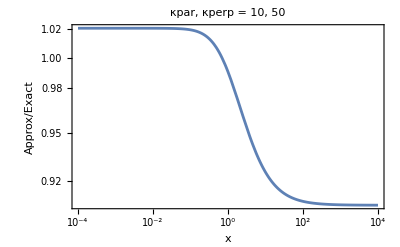
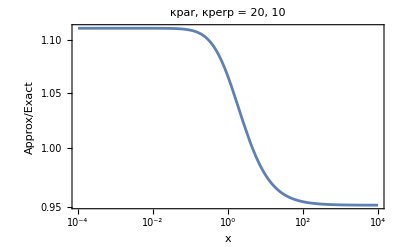
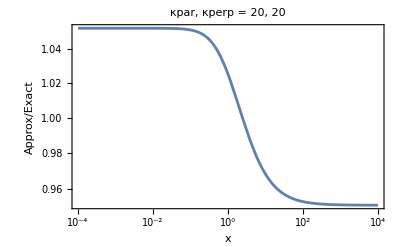
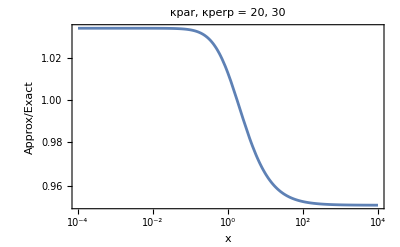

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

Exact[x_,κperp_,κpar_]:=κperp*Hypergeometric2F1[1,κpar+0.5,κpar+κperp+1.5,1-κperp/κpar*x]/(κperp+κpar+0.5);
approx[x_,κperp_,κpar_]:=κperp*(Exp[1-κperp/κpar*x*(κpar+0.5)-κperp]-1)/(1-κperp/κpar*x*(κpar+0.5)-κperp);
ratio[x_,κperp_,κpar_]:=approx[x,κperp,κpar]/Exact[x,κperp,κpar];
Table[Plot[ratio[x,κperp,κpar],{x,0.0001,10000},Frame->True,FrameLabel->{"x","Approx/Exact"},PlotLabel->"κpar, κperp = " <> ToString[κpar]<>", "<>ToString[κperp],ScalingFunctions->{"Log10","Log10"}],{κpar,10,50,10},{κperp,10,50,10}]
```

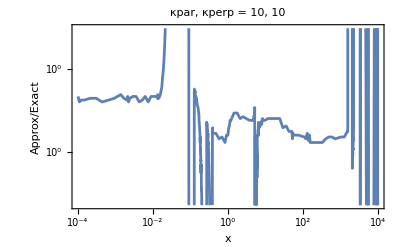
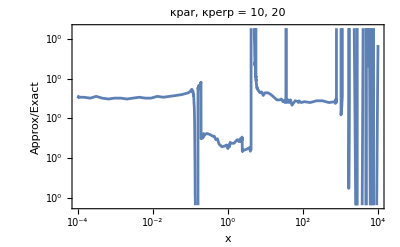
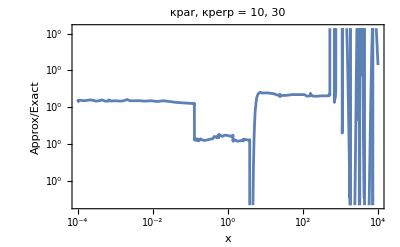
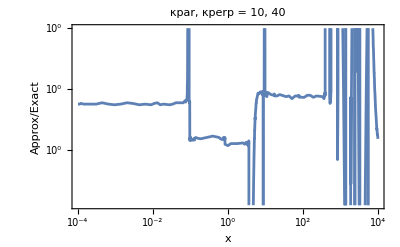
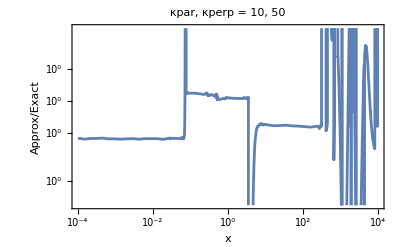
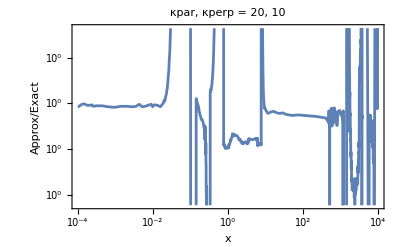
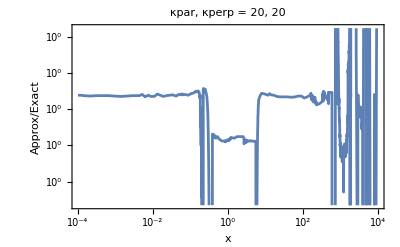
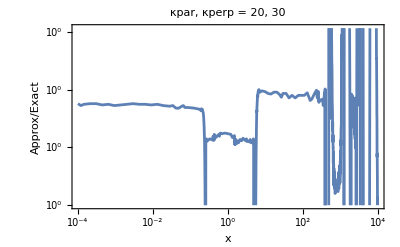

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

Exact[x_,κperp_,κpar_]:=Hypergeometric2F1[1,κpar+0.5,κpar+κperp+1.5,1-κperp/κpar*x]/(κperp+κpar+0.5);
approx[z_,κperp_,κpar_]:=NIntegrate[(1-t)^(κpar+κperp-1/2)*(1-t*z)^(-(κpar+1/2)),{t,0,1}]
ratio[x_,κperp_,κpar_]:=approx[1-κperp/κpar*x,κperp,κpar]/Exact[x,κperp,κpar]
Table[Plot[ratio[x,κperp,κpar],{x,0.0001,10000},Frame->True,FrameLabel->{"x","Approx/Exact"},PlotLabel->"κpar, κperp = " <> ToString[κpar]<>", "<>ToString[κperp],ScalingFunctions->{"Log10","Log10"}],{κpar,10,50,10},{κperp,10,50,10}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

Exact[x_,κperp_,κpar_]:=κperp*Hypergeometric2F1[1,κpar+0.5,κpar+κperp+1.5,1-κperp/κpar*x]/(κperp+κpar+0.5);
approx[x_,κperp_,κpar_]:=κperp*(Exp[1-κperp/κpar*x*(κpar+0.5)-κperp]-1)/(1-κperp/κpar*x*(κpar+0.5)-κperp);
ratio[x_,κperp_,κpar_]:=approx[x,κperp,κpar]/Exact[x,κperp,κpar];
Table[Plot[ratio[x,κperp,κpar],{x,0.0001,10000},Frame->True,FrameLabel->{"x","Approx/Exact"},PlotLabel->"κpar, κperp = " <> ToString[κpar]<>", "<>ToString[κperp],ScalingFunctions->{"Log10","Log10"}],{κpar,100,600,200},{κperp,100,600,200}]
```

General::munfl: 0.000100038^100 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.1543×10^-306 0.000100038 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(6.74309×10^-306)/1131 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

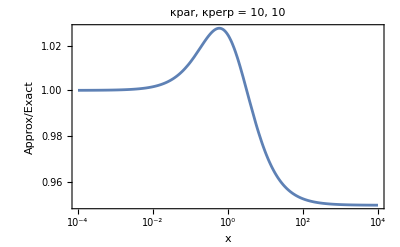
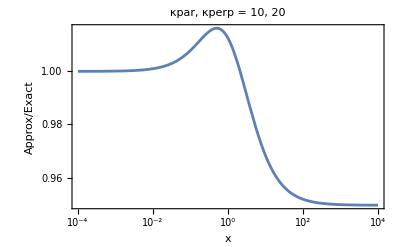
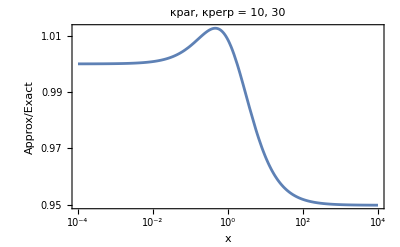
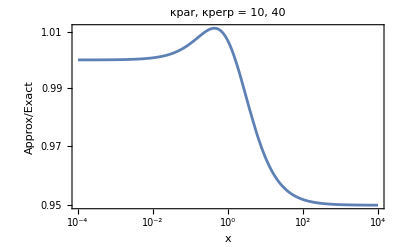
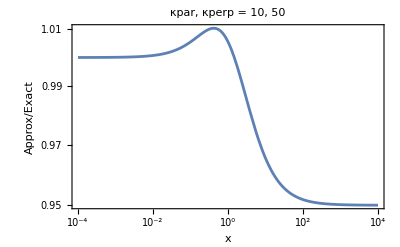
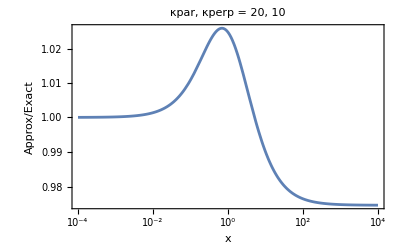
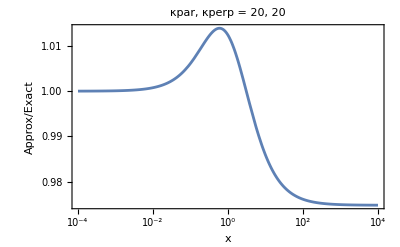
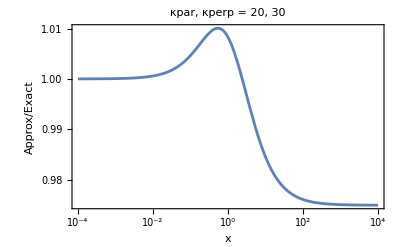

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

Exact[x_,κperp_,κpar_]:=Hypergeometric2F1[1,κpar+0.5,κpar+κperp+1.5,1-κperp/κpar*x]/(κperp+κpar+0.5);
approx[x_,κperp_,κpar_]:=1/(κperp*x+κperp);
ratio[x_,κperp_,κpar_]:=approx[x,κperp,κpar]/Exact[x,κperp,κpar];
Table[Plot[ratio[x,κperp,κpar],{x,0.0001,10000},Frame->True,FrameLabel->{"x","Approx/Exact"},PlotLabel->"κpar, κperp = " <> ToString[κpar]<>", "<>ToString[κperp],ScalingFunctions->{"Log10","Log10"}],{κpar,10,50,10},{κperp,10,50,10}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*NIntegrate[(1-t)^(κpar+κperp-1/2)*(1-t*z)^(-(κpar+1/2)),{t,0,1}]*)
Limit[(1-t)^(κpar+κperp-1/2)*(1-t*(1-κperp*x/κpar))^(-(κpar+1/2)),κpar->Infinity,Assumptions->{0<=t<=1,x>=0,κperp>1}]
```

ⅇ^((t x κperp)/(-1+t)) (1-t)^(-1+κperp)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Integrate[ⅇ^((t x κperp)/(-1+t)) (1-t)^(-1+κperp),{t,0,1},Assumptions->{κperp>1.,x>=0}]
```

ⅇ^(x κperp) ExpIntegralE[1+κperp,x κperp]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*NIntegrate[(1-t)^(κpar+κperp-1/2)*(1-t*z)^(-(κpar+1/2)),{t,0,1}]*)
Limit[κperp*(1+ΔPE/(κpar*Tpar))^(-(κpar+1/2))*(1-t)^(κpar+κperp-1/2)*(1-t*(1-κperp*x/κpar))^(-(κpar+1/2)),κperp->Infinity,Assumptions->{0<=t<=1,x>=0,κpar>0.5,ΔPE/(κpar*Tpar)>-1,Tpar>0}]
```

0

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={n>0,κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,ΔPE/(κpar0*Tpar0)>-1,B>=B0,ΔPE∈Reals,0<d<1,m>0};
n=n0/d*((κperp0*(1+ΔPE/(κpar0*Tpar0))^(-(κpar0 + 1/2))*κperp0*1/(κpar0+kperp0+1/2)Hypergeometric2F1[1,κpar0+1/2,κpar0+kperp0+3/2,1-κperp0/κpar0*Tperp0/Tpar0*(B/B0-1)/(1+ΔPE/(κpar0*Tpar0))]));
C0=(m^(3/2) n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar0) Gamma[1/2+κpar0])
FullSimplify[C0*2*Pi/(2*n)*m*Integrate[vperp^3*((1+ (m*vperp^2*d)/(2*κperp0*Tperp0))^(-(κperp0+1)))*(1+((1/2)*m*vpar^2+(1/2)*m*vperp^2*(1-d)+ΔPE)/(κpar0*Tpar0))^(-(κpar0+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[C0*2*Pi/n*m*Integrate[vperp*vpar^2*((1+ (m*vperp^2*d)/(2*κperp0*Tperp0))^(-(κperp0+1)))*(1+((1/2)*m*vpar^2+(1/2)*m*vperp^2*(1-d)+ΔPE)/(κpar0*Tpar0))^(-(κpar0+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

(m^(3/2) n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar0) Gamma[1/2+κpar0])

Integrate::idiv: Integral of TerminatedEvaluation[RecursionLimit] does not converge on {-∞,∞}.

(d m^(5/2) (1+ΔPE/(Tpar0 κpar0))^(1/2+κpar0) (1+2 kperp0+2 κpar0) Gamma[1+κpar0] Integrate[TerminatedEvaluation[RecursionLimit],{vpar,-∞,∞},Assumptions→n0 (1+2 kperp0+2 κpar0) Hypergeometric2F1[1,1/2+κpar0,3/2+kperp0+κpar0,1+((-B+B0) Tperp0 κperp0)/(B0 (ΔPE+Tpar0 κpar0))]>0])/(4 √(2 π) Tperp0 √(Tpar0 κpar0) κperp0^2 Gamma[1/2+κpar0] Hypergeometric2F1[1,1/2+κpar0,3/2+kperp0+κpar0,1+((-B+B0) Tperp0 κperp0)/(B0 (ΔPE+Tpar0 κpar0))])

Integrate::idiv: Integral of vpar^2 TerminatedEvaluation[RecursionLimit] does not converge on {-∞,∞}.

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={n>0,κpar>1/2,κperp>1,Tpar>0,Tperp>0,m>0}

FullSimplify[Solve[n==A*2*Pi*Integrate[vperp*((1+ (m*vperp^2)/(2*κperp*Tperp))^(-(κperp+1)))*(1+(m*vpar^2)/(2*κpar*Tpar))^(-(κpar+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],A,Assumptions->assumps],assumps]
```

{n>0,κpar>1/2,κperp>1,Tpar>0,Tperp>0,m>0}

{{A→(m^(3/2) n Gamma[1+κpar])/(2 √2 π^(3/2) Tperp √(Tpar κpar) Gamma[1/2+κpar])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={n>0,κpar>1/2,κperp>1,Tpar>0,Tperp>0,m>0}
C0=(m^(3/2) n Gamma[1+κpar])/(2 √2 π^(3/2) Tperp √(Tpar κpar) Gamma[1/2+κpar]);
FullSimplify[C0*2*Pi/(2*n)*m*Integrate[vperp^3*((1+ (m*vperp^2)/(2*κperp*Tperp))^(-(κperp+1)))*(1+(m*vpar^2)/(2*κpar*Tpar))^(-(κpar+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[C0*2*Pi/n*m*Integrate[vperp*vpar^2((1+ (m*vperp^2)/(2*κperp*Tperp))^(-(κperp+1)))*(1+(m*vpar^2)/(2*κpar*Tpar))^(-(κpar+1)),{vpar,-Infinity,Infinity},{vperp,0,Infinity},Assumptions->assumps],assumps]
```

{n>0,κpar>1/2,κperp>1,Tpar>0,Tperp>0,m>0}

(Tperp κperp)/(-1+κperp)

(2 Tpar κpar)/(-1+2 κpar)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={n>0,κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,ΔPE/(κpar0*Tpar0)>-1,B>=B0,ΔPE∈Reals,E0∈Reals,E0/(κpar0*Tpar0)>-1,m>0};
n=n0*d*(κperp0*(1+ΔPE/(κpar0*Tpar0))^(-(κpar0 + 1/2))*κperp0*1/(κpar0+kperp0+1/2)Hypergeometric2F1[1,κpar0+1/2,κpar0+kperp0+3/2,1-κperp0/κpar0*Tperp0/Tpar0*(B/B0-1)/(1+ΔPE/(κpar0*Tpar0))]);
C0=(m^(3/2) n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar0) Gamma[1/2+κpar0]);
Integrate[(1+((1/2)*m*vpar^2+E0)/(κpar0*Tpar0))^(-(κpar0+1)),{vpar,-Infinity,Infinity},Assumptions->assumps]
Integrate[vpar^2*(1+((1/2)*m*vpar^2+E0)/(κpar0*Tpar0))^(-(κpar0+1)),{vpar,-Infinity,Infinity},Assumptions->assumps]
```

(√(2 π) Tpar0 ((Tpar0 κpar0)/(E0+Tpar0 κpar0))^κpar0 Gamma[1/2+κpar0])/(√(m (E0+Tpar0 κpar0)) Gamma[κpar0])

(√(2 π) Tpar0 (Tpar0 κpar0)^κpar0 (E0+Tpar0 κpar0)^(1/2-κpar0) Gamma[-1/2+κpar0])/(m^(3/2) Gamma[κpar0])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={n>0,κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,ΔPE/(κpar0*Tpar0)>-1,B>=B0,ΔPE∈Reals,0<d<1,m>0};
n=n0/d*((κperp0*(1+ΔPE/(κpar0*Tpar0))^(-(κpar0 + 1/2))*κperp0*1/(κpar0+kperp0+1/2)Hypergeometric2F1[1,κpar0+1/2,κpar0+kperp0+3/2,1-κperp0/κpar0*Tperp0/Tpar0*(B/B0-1)/(1+ΔPE/(κpar0*Tpar0))]));
C0=(m^(3/2) n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar0) Gamma[1/2+κpar0])
FullSimplify[C0*2*Pi/(2*n)*m*Integrate[vperp^3*((1+ (m*vperp^2*d)/(2*κperp0*Tperp0))^(-(κperp0+1)))*(√(2 π) Tpar0 ((Tpar0 κpar0)/(E0+Tpar0 κpar0))^κpar0 Gamma[1/2+κpar0])/(√(m (((1/2)*m*vperp^2*(1-d)+ΔPE)+Tpar0 κpar0)) Gamma[κpar0]),{vperp,0,Infinity},Assumptions->assumps],assumps]
FullSimplify[C0*2*Pi/n*m*Integrate[vperp*((1+ (m*vperp^2*d)/(2*κperp0*Tperp0))^(-(κperp0+1)))*1/(m^(3/2) Gamma[κpar0])√(2 π) Tpar0 (Tpar0 κpar0)^κpar0 (((1/2)*m*vperp^2*(1-d)+ΔPE)+Tpar0 κpar0)^(1/2-κpar0) Gamma[-1/2+κpar0],{vperp,0,Infinity},Assumptions->assumps],assumps]
```

(m^(3/2) n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √(Tpar0 κpar0) Gamma[1/2+κpar0])

(d m^2 (1+2 kperp0+2 κpar0) (1/(E0+Tpar0 κpar0))^κpar0 (ΔPE+Tpar0 κpar0)^(1/2+κpar0) TerminatedEvaluation[RecursionLimit])/(4 Tperp0 κperp0^2 Hypergeometric2F1[1,1/2+κpar0,3/2+kperp0+κpar0,1+((-B+B0) Tperp0 κperp0)/(B0 (ΔPE+Tpar0 κpar0))])

(d m (1+2 kperp0+2 κpar0) (ΔPE+Tpar0 κpar0)^(1/2+κpar0) TerminatedEvaluation[RecursionLimit])/(Tperp0 (-1+2 κpar0) κperp0^2 Hypergeometric2F1[1,1/2+κpar0,3/2+kperp0+κpar0,1+((-B+B0) Tperp0 κperp0)/(B0 (ΔPE+Tpar0 κpar0))])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*contrary to before d = B/B0>1*)
assumps={Tpar>0,Tperp>0,A>0,κpar>0.5,κperp>1,λ>0,d>1,ΔPE∈Reals,ΔPE/(κpar*Tpar)>-1,n0>0}
x=λ*A*(d-1)/(ΔPE/(κpar*Tpar)+1);
f=n0*d*(ΔPE/(κpar*Tpar)+1)^(-1/2-κpar)*1/(λ+1.5)λ*Hypergeometric2F1[1,κpar+0.5,κpar+κperp+1.5,1-λ*A*(d-1)/(ΔPE/(κpar*Tpar)+1)]
```